```mathematica
Clear["Global`*"]
f[r_,θ_]=μ*r-r^3;
g[r_,θ_]=ω+ν*r^2;
Solve[f[r,θ]==0,{r,θ}]
v= g[Sqrt[μ],0] (*v=ω*r*)
T=2*π/v(*s=v*t*)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{r→0},{r→-√μ},{r→√μ}}

μ ν+ω

(2 π)/(μ ν+ω)

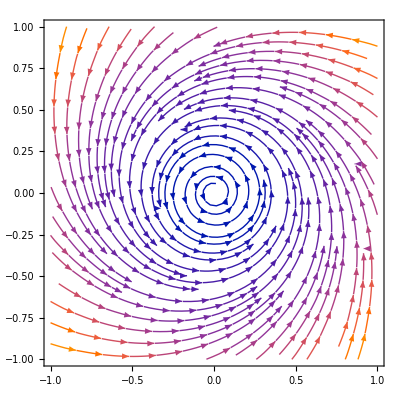

```mathematica
Clear["Global`*"]
X1[r_, θ_] = r*Cos[θ];
X2[r_, θ_] = r*Cos[θ];
F1[X1_, X2_] = 1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
F2[X1_, X2_] = X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;
StreamPlot[{F1[X1,X2],F2[X1,X2]},{X1,-1,1},{X2,-1,1}]
```